```mathematica
eps=10^-6;
domainY=3;
domainX=4;
samples=40;
major=8;
i[x_, y_]:= ((2BesselJ[1, √(x^2+y^2)*Pi+eps])/(√(x^2+y^2)*Pi+eps))^2;
createData[d_]:=Flatten[Table[Join[Table[{SetPrecision[x,3],SetPrecision[y,3],SetAccuracy[i[x+d/2, y]+i[x-d/2,y],4] },{x, -domainX, domainX, domainX/samples}],{{}}],{y, domainY, -domainY, -domainY/samples}],1];
dataAll=createData[1.22];
data = Join[{{"x", "y" ,"I"}}, dataAll];

dataY=
Join[
{{"x", "y" ,"I"}},
Table[
{SetPrecision[x,3] ,0,SetAccuracy[i[x+0.61, 0]+i[x-0.61,0],4] }, {x, -domainX, domainX, domainX/samples}
]];

dataX=Join[{{"x", "y" ,"I"}}, Table[{0.61,SetPrecision[y,3],SetAccuracy[i[1.22, y]+i[0,y],4] }, {y, -domainY, domainY, domainY/samples}]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk.txt"}], data, "Table"];
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-y.txt"}], dataY, "Table"];
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-x.txt"}], 
dataX, "Table"];
```

```mathematica
createData[distance_]:=Flatten[Table[Table[{N[x,3] ,N[y,3],i[x+distance/2, y]+i[x-distance/2,y] }, {x, -domainX, domainX, 0.1}], {y, domainY, -domainY, -0.1}],1];
```

```mathematica
Table[Export[FileNameJoin[{NotebookDirectory[],"..","img","eiry-disk-"<>ToString[d]<>".png"}],
ListDensityPlot[createData[1.22*d], ColorFunction->GrayLevel,Frame->None, AspectRatio->3/4, ImageSize->800],"Image"] ,{d, 1, 3}];
```

Options::optnf: ImageResolution is not a known option for Graphics.

General::stop: Further output of Options::optnf will be suppressed during this calculation.

```mathematica
eiry[x_,diff_]:=((2BesselJ[1, (x-0.61diff)*Pi+eps])/((x-0.61diff)*Pi+eps))^2+((2BesselJ[1, (x+0.61diff)*Pi+eps])/((x+0.61diff)*Pi+eps))^2;
data=Table[Join[{SetAccuracy[x,3], SetAccuracy[((2BesselJ[1, x*Pi+eps])/(x*Pi+eps))^2,4]},Table[SetAccuracy[eiry[x,d],4],{d,1,3,1}]],{x,-4,4,0.05}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-profile.txt"}],Join[{{"x", "e0","e1","e2","e3"}},data],"Table"];
```

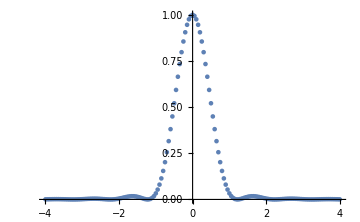
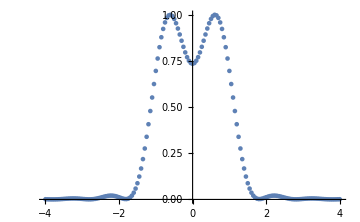
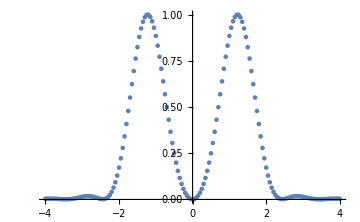
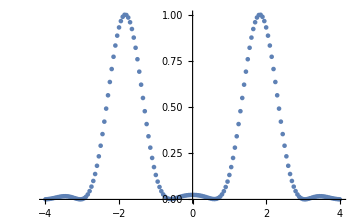

```mathematica
Table[ListPlot[Table[{data[[i]][[1]],data[[i]][[j + 1]]},{i,1,Length@data}], PlotRange->All, ImageSize->Medium],{j,1,4}]
```